```mathematica
n:={Cos[ϕ],Sin[ϕ],0}/.{ϕ->ϕ[x]}
```

```mathematica
bend:=1/2 K11 Div[n,{x,y,z}]^2//FullSimplify
twist:=1/2 K22(n.Curl[n,{x,y,z}])^2//FullSimplify
splay:=1/2 K33(Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]])//Simplify
```

```mathematica
(*elastic energy*)
fgOF=twist+bend+splay/.K33->K11//Simplify
```

1/2 K11 ϕ'[x]^2

```mathematica
(*anchoring energy at ϕ[x==xf] is ϕf*)
fgS=-Ws ({Wx,Wy,Wz}.n)^2/.{ϕ[x]->ϕf,Wx->1/Sqrt[2],Wy->1/Sqrt[2],Wz->0}//Simplify
```

-1/2 Ws (1+Sin[2 ϕf])

```mathematica
(*assume the twist is linear (I can prove this but I don't feel like it):*)
ϕlin[x_]:=π/2+(ϕf-π/2) x/xf
ϕlin[0]
ϕlin[xf]
```

π/2

ϕf

```mathematica
(*The energy through the bulk is*)
1/2 K11 D[ϕlin[x],x]^2//Simplify
(*Integrated through the bulk, the total energy per unit area is*)
Integrate[%,{x,0,xf}]//Simplify
(*This total energy changes with ϕf, so the bulk applies a torque on ϕf that looks like this:*)
-D[%,ϕf]//Simplify
```

(K11 (π-2 ϕf)^2)/(8 xf^2)

(K11 (π-2 ϕf)^2)/(8 xf)

(K11 (π-2 ϕf))/(2 xf)

```mathematica
(*The surface energy changes like so with ϕf*)
-D[fgS,ϕf]
```

Ws Cos[2 ϕf]

```mathematica
(*The system is at equilibrium when the two torques add to 0. Make a function to find the equilibrium value of ϕf that solves the nonlinear torque balance equation. Notice that there is actually only one variable that matters: the dimensionless ratio Ws*xf/K11 (this should sound familiar). The stuff happens when this thing is around 1. I will leave this function in terms of three variables for clarity though.*)
findequilibriumϕf[Ws_,K11_,xf_]:=ϕf/.FindRoot[(K11 (π-2 ϕf))/(2 xf)+Ws Cos[2 ϕf]==0,{ϕf,1.2}]
```

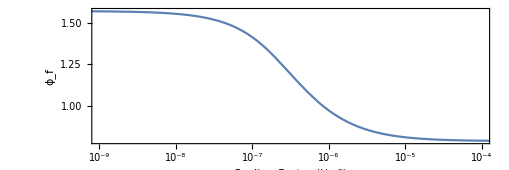

```mathematica
Quiet@LogLinearPlot[findequilibriumϕf[Ws,12*^-12,20*^-6],{Ws,10^-10,10^-3},PlotRange->{{10^-9,10^-4},Automatic},AspectRatio->1/3,FrameLabel->(Style[#,SingleLetterItalics->False]&/@{"Scaling Factor (J/m^2)","ϕ_f"}),RotateLabel->False,GridLines->{{12/20*10^-6},{π/4,π/2}}]
```